```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Caden Gobat\Documents\GitHub\PHYS-3181\homework3

```mathematica
startingEnergy=0.5*(6.283)^2-4*Pi^2
```

-19.7404

```mathematica
orbitalEnergies=Abs[ReadList["halfyearenergies.log",{Number,Number}]]
```

{{0.0001,19.7404},{0.0003,19.7404},{0.001,19.7404},{0.003,19.7403},{0.01,19.7386},{0.03,19.706},{0.1,19.3917}}

```mathematica
afterhalfyear=orbitalEnergies[[;;,2]]
```

{19.7404,19.7404,19.7404,19.7403,19.7386,19.706,19.3917}

```mathematica
deltaE=afterhalfyear+startingEnergy
```

{-2.61185×10^-9,-5.80126×10^-8,-1.97492×10^-6,-0.0000511875,-0.00173091,-0.0344044,-0.348699}

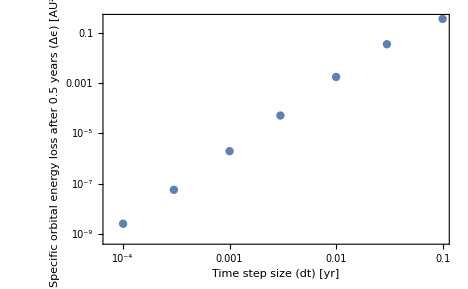

```mathematica
ListLogLogPlot[Transpose@{orbitalEnergies[[;;,1]],Abs[deltaE]},Frame->True,FrameLabel->{"Time step size (dt) [yr]","Specific orbital energy loss after 0.5 years (Δϵ) [AU^2/yr^2]"}]
```

```mathematica
N[(Log[Last[Abs[deltaE]]]-Log[First[Abs[deltaE]]])/(Log[Last[orbitalEnergies[[;;,1]]]]-Log[First[orbitalEnergies[[;;,1]]]])]
```

2.7085

```mathematica
orbitData=ReadList["orbit.log",{Number,Number,Number,Number,Number}];
```

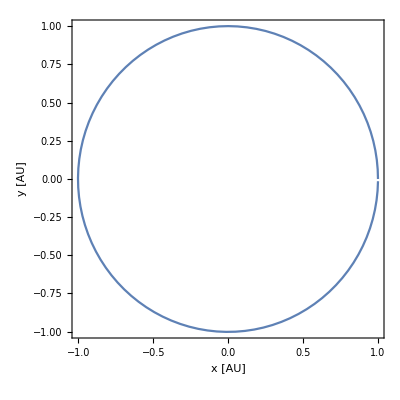

```mathematica
ListLinePlot[orbitData[[;;,{2,3}]],Frame->True,FrameLabel->{"x [AU]","y [AU]"},AspectRatio->1]
```

```mathematica
ellipticalOrbit=ReadList["q3orbit.log",{Number,Number,Number,Number,Number}];
```

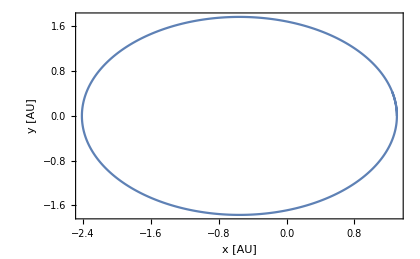

```mathematica
ListLinePlot[ellipticalOrbit[[;;,{2,3}]],Frame->True,FrameLabel->{"x [AU]","y [AU]"}]
```

```mathematica
ellipticalEnergy=ReadList["q3energy.log",{Number,Number,Number}]
```

{{0.,19.738,-30.3679},{0.001,19.7377,-30.3677},{0.002,19.7373,-30.3673},{0.003,19.7367,-30.3667},{0.004,19.736,-30.366},{0.005,19.7351,-30.3651},{0.006,19.734,-30.364},{0.007,19.7328,-30.3628},{0.008,19.7314,-30.3614},{0.009,19.7299,-30.3598},{0.01,19.7282,-30.3581},{0.011,19.7263,-30.3562},5177,{5.189,18.4876,-29.1175},{5.19,18.4698,-29.0997},{5.191,18.4519,-29.0818},{5.192,18.4339,-29.0639},{5.193,18.4158,-29.0458},{5.194,18.3977,-29.0276},{5.195,18.3794,-29.0094},{5.196,18.3611,-28.9911},{5.197,18.3427,-28.9727},{5.198,18.3242,-28.9542},{5.199,18.3056,-28.9356}}
 |  |  |  |

```mathematica
R=Sqrt[ellipticalOrbit[[;;,2]]^2+ellipticalOrbit[[;;,3]]^2];
Max[R]/Min[R]
```

1.85683

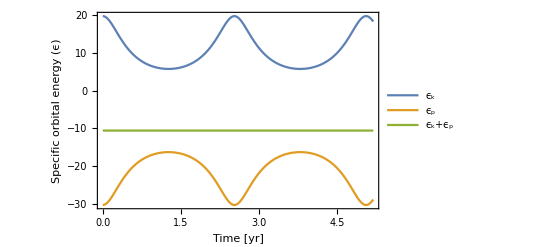

```mathematica
energyplot=ListLinePlot[{ellipticalEnergy[[;;,{1,2}]],ellipticalEnergy[[;;,{1,3}]],Transpose@{ellipticalEnergy[[;;,1]],ellipticalEnergy[[;;,2]]+ellipticalEnergy[[;;,3]]}},PlotLegends->{"ϵ_k","ϵ_p","ϵ_k+ϵ_p"},Frame->True,FrameLabel->{"Time [yr]","Specific orbital energy (ϵ)"}]
```

```mathematica
Export["q3energy.pdf",energyplot]
```

q3energy.pdf

```mathematica
cometOrbit=ReadList["q4orbit.log",{Number,Number,Number,Number,Number}]
```

{{0.,1.995,0.,0.,6.283},{0.001,1.995,0.006283,-0.0099191,6.28298},{0.101,1.94524,0.62935,-0.96951,6.13007},{0.201,1.80663,1.22434,-1.76691,5.74069},{0.301,1.59946,1.7739,-2.33911,5.24253},{0.401,1.34554,2.2727,-2.71019,4.73799},{0.501,1.06232,2.72303,-2.93418,4.27813},76928,{7693.4,0.987763,-2.82962,2.9736,4.17146},{7693.5,1.27627,-2.39071,2.77845,4.61669},{7693.6,1.53901,-1.90455,2.44973,5.11299},{7693.7,1.75992,-1.36768,1.93265,5.62033},{7693.8,1.91796,-0.783036,1.19048,6.04935},{7693.9,1.99159,-0.164722,0.259624,6.27228}}
 |  |  |  |

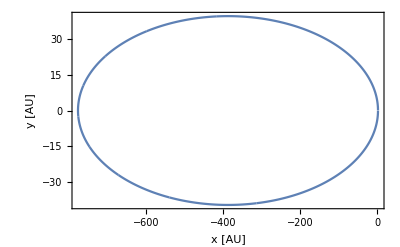

```mathematica
q4comet=ListLinePlot[cometOrbit[[;;,{2,3}]],Frame->True,FrameLabel->{"x [AU]","y [AU]"}]
```

```mathematica
Export["q4orbit.pdf",q4comet]
```

q4orbit.pdf

```mathematica
cometEnergy=ReadList["q4energy.log",{Number,Number,Number}]
```

{{0.,19.738,-19.7886},{0.1,19.2588,-19.3095},{0.2,18.0387,-18.0894},{0.3,16.4778,-16.5284},{0.4,14.8969,-14.9475},{0.5,13.4559,-13.5066},{0.6,12.2031,-12.2538},{0.7,11.1338,-11.1845},{0.8,10.2249,-10.2756},{0.9,9.45027,-9.50092},{1.,8.786,-8.83665},{1.101,8.20688,-8.25753},76917,{7692.9,8.6334,-8.68404},{7693.,9.27311,-9.32376},{7693.1,10.0178,-10.0685},{7693.2,10.8904,-10.9411},{7693.3,11.9168,-11.9674},{7693.4,13.1217,-13.1723},{7693.5,14.5168,-14.5675},{7693.6,16.0719,-16.1226},{7693.7,17.6617,-17.7123},{7693.8,19.0059,-19.0566},{7693.9,19.7045,-19.7551}}
 |  |  |  |

```mathematica
ListLinePlot[{cometEnergy[[;;,{1,2}]],cometEnergy[[;;,{1,3}]],Transpose@{cometEnergy[[;;,1]],cometEnergy[[;;,2]]+cometEnergy[[;;,3]]}},PlotLegends->{"ϵ_k","ϵ_p","ϵ_k+ϵ_p"},Frame->True,FrameLabel->{"Time [yr]","Specific orbital energy (ϵ)"}]
```

-Graphics-

```mathematica
Export["q4energy.pdf",energyplot]
```

q4energy.pdf

```mathematica
longcometOrbit=ReadList["q5orbit.log",{Number,Number,Number,Number,Number}]
```

{{0.,1.995,0.,0.,6.283},{0.05,1.9826,0.31415,-0.491381,6.24431},{5.1,-10.8811,10.0551,-2.12445,0.814725},{10.05,-20.2015,13.1116,-1.7003,0.484981},{15.05,-28.1079,15.1736,-1.4811,0.354964},{20.05,-35.1391,16.7546,-1.34005,0.283322},{25.05,-41.5731,18.0482,-1.23844,0.237057},5988,{29970.1,-1067.23,79.9274,-0.0628451,-0.00700754},{29975.1,-1067.54,79.8923,-0.0626733,-0.00702041},{29980.1,-1067.86,79.8571,-0.0625015,-0.00703325},{29985.1,-1068.17,79.8219,-0.0623299,-0.00704608},{29990.1,-1068.48,79.7867,-0.0621584,-0.00705889},{29995.1,-1068.79,79.7514,-0.061987,-0.00707169}}
 |  |  |  |

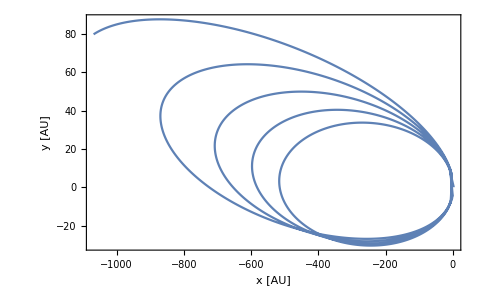

```mathematica
longorbitplot=ListLinePlot[longcometOrbit[[;;,{2,3}]],Frame->True,FrameLabel->{"x [AU]","y [AU]"}]
```

```mathematica
Export["q5orbit.pdf",longorbitplot]
```

q5orbit.pdf